```mathematica
<< Units`
```

```mathematica
Needs["PhysicalConstants`"]
```

## Helmholtz Coil Design Specifications

### Initial conditions

```mathematica
d=x Inch (* coil diameter *)
```

Inch x

```mathematica
Subscript[r, 1] = (1.5 Inch)/2 (* coil innner radius *)
```

0.75 Inch

```mathematica
n =. (* number of turns per coil *)
```

```mathematica
B=0.3 Tesla (* desired magnetic field *)
```

0.3 Tesla

### Geometric calculations

#### Circle packing density is roughly 0.9, so the area occupied by N turns with diameter d each is:

```mathematica
A=n 1/0.9 Pi (d/2)^2
```

0.872665 Inch^2 n x^2

#### This area corresponds to a circular bundle with radius

```mathematica
Subscript[r, 2]=Sqrt[A/Pi]
```

0.527046 √(Inch^2 n x^2)

#### Therefore, the effective radius of the Helmholtz coil is

```mathematica
Subscript[r, 3]=Convert[Subscript[r, 1]+Subscript[r, 2], Meter]
```

Meter (0.013387 √(n x^2)+0.01905)

### Magnetics calculations

#### To achieve our desired magentic field, B, we need a current I_1 running through our coil:

```mathematica
Subscript[I, 1] = (B Subscript[r, 3])/(n VacuumPermeability) (4/5)^(-(3/2))
```

(333639. Ampere Meter^2 Tesla (0.013387 √(n x^2)+0.01905))/(n Second Volt)

```mathematica
Convert[Subscript[I, 1], Ampere]
```

(333639. Ampere (0.013387 √n x+0.01905))/n

### Power calculations

#### The resistivity of copper

```mathematica
Subscript[rho, c]=1.7*10^-8 Ohm Meter
```

1.7×10^-8 Meter Ohm

#### And the total length of wire is

```mathematica
l=n 2 Pi Subscript[r, 3]
```

2 π Meter n (0.013387 √(n x^2)+0.01905)

#### So the resistance of the wire is

```mathematica
R =Convert[(Subscript[rho, c] l)/(Pi (d/2)^2), Ohm]
```

(0.0002108 n Ohm (0.013387 √n x+0.01905))/x^2

#### And the voltage and power for each coil are:

```mathematica
V = Convert[Subscript[I, 1] R, Volt]
```

(70.3312 Volt (0.013387 √n x+0.01905)^2)/x^2

```mathematica
P = Convert[Subscript[I, 1] V, Watt]
```

(2.34652×10^7 Watt (0.013387 √n x+0.01905)^3)/(n x^2)

```mathematica
HelmholtzPower[xin_, nin_]:=With[{x=xin, n=nin}, P]
```

## Results

```mathematica
Manipulate[Evaluate[HelmholtzPower[x, n]], {x, 0.01, 0.1}, {n, 100, 2000}]
(* x is the wire diameter in inches, n is the number of turns *)
```

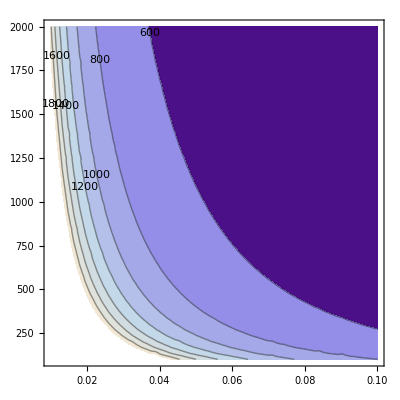

```mathematica
ContourPlot[HelmholtzPower[x, n]/Watt, {x, 0.01, 0.1}, {n, 100, 2000},ContourLabels->True]
```

## A reasonable solution

```mathematica
Block[{x=0.0641, n=600}, Print[Evaluate[P]];
Print[Evaluate[Convert[Subscript[I, 1],Ampere]]];
Print[Evaluate[Convert[Subscript[I, 1] R, Volt]]]]
```

612.335 Watt

22.2811 Ampere

27.4823 Volt